```mathematica
B=0.368
```

0.368

```mathematica
A=-130
```

-130

```mathematica
Y=A/B
```

-353.261

```mathematica
p=-4*A*B(0.212/600+0.368/1300+0.273/2000+0.133/2700)
```

0.15733

```mathematica
q=-4*B*B(0.212/600+0.368/1300+0.273/2000+0.133/2700)
```

-0.000445366

```mathematica
X[J_]:=Abs[Sqrt[Y*(Y-4)+(J+1/2)^2]]
```

```mathematica
DV[J_]:=((p/2+q)*(-1+2/X[J]-Y/X[J])+(2*q)/X[J]*(J-0.5)*(J+1.5))*(J+0.5)
```

```mathematica
Z=Table[{J,DV[J]*3*10^4},{J,1.5,9.5,1}];
```

```mathematica
MatrixForm[Z]
```

(1.5 | -0.451307
2.5 | -1.94463
3.5 | -4.95905
4.5 | -10.0014
5.5 | -17.5783
6.5 | -28.1963
7.5 | -42.3615
8.5 | -60.5798
9.5 | -83.3568)

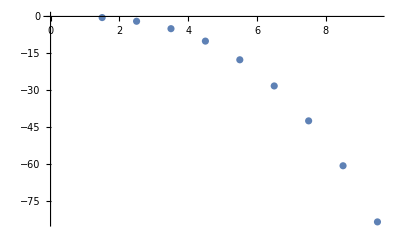

```mathematica
ListPlot[Z]
```